# Using IFS to Reveal Biases in the Distribution of Prime Numbers

Harlan J. Brothers

This is a Mathematica notebook to accompany the paper:
“Using IFS to Reveal Biases in the Distribution of Prime Numbers” by Harlan J. Brothers. It appears in the journal Fractals, Vol. 32, No. 06 (2024):
https://www.worldscientific.com/doi/10.1142/S0218348X24501032

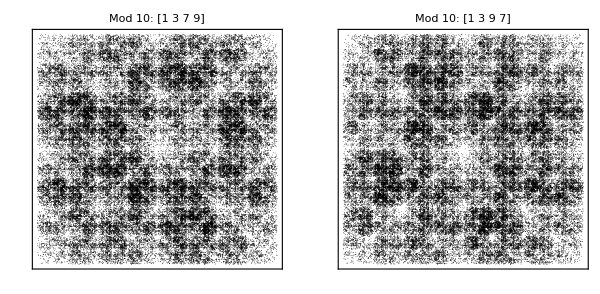

```mathematica
divider=2;(* Sets grid divisions for x and y *)
grid=Table[k/divider,{k,1,divider-1}];
coPrime[k_]:=Select[Range[k],CoprimeQ[#,k]&];
perm={{1,2,3,4},{1,2,4,3}};

(* Function to generate IFS plots *)
ifsPlots:=Module[{cp,plts,transformOrder,f,pt,ptlst,createPlot},
If[!MemberQ[{5,8,10,12},mod],Print[Style["Please choose a modulus of either 5, 8, 10, or 12.",14]];Return[]];
cp=coPrime[mod];
transformOrder[permList_]:=Switch[Mod[#,mod],cp[[1]],permList[[1]],cp[[2]],permList[[2]],cp[[3]],permList[[3]],cp[[4]],permList[[4]]]&/@Prime[Range[start,start+end-1]];
f[j_,{x_,y_}]:=0.5*{x,y}+0.5*Reverse[IntegerDigits[j-1,2,2]];
createPlot[permIdx_]:=Module[{trOrder,pt,ptlst},trOrder=transformOrder[perm[[permIdx]]];
pt={0.5,0.5};
ptlst=Table[pt=f[trOrder[[j]],pt],{j,Length[trOrder]}];
ListPlot[ptlst,
Frame->True,
FrameStyle->Directive[RGBColor[0,0.5,0.8],Thickness[0.006]],
FrameTicks->None,
Axes->True,
GridLines->{grid,grid},
GridLinesStyle->Directive[RGBColor[0,0.5,0.8],Thickness[0.002]],
PlotRange->{{0,1},{0,1}},
PlotStyle->{PointSize[ptSize],Black},
AspectRatio->1,
PlotLabel->Style["Mod "<>ToString@mod<>": ["<>StringJoin@Riffle[ToString/@cp[[perm[[permIdx]]]]," "]<>"]",13],ImageSize->imgSize]];
plts=Table[createPlot[i],{i,2}];
GraphicsRow[plts,Spacings->12,ImageSize->2imgSize]]

(* Parameters *)
start=4;
end=100000;
imgSize=300;
ptSize=0.001;
mod=10;

(* Execute function *)
ifsPlots
```